```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]

g=9.81;
r=53/2*10^(-3);
e=12*10^(-3);
m=0.375;
J3=0.000055;
J1=0.000055;
h=31.25*10^(-3);
x0 = 2.5*10^(-2);
```

```mathematica
EquationForced = {
(J1 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-J1 D[θ[t],{t, 2}]-J3 Sin[θ[t]] D[ϕ[t],t] D[ψ[t],t]-(J3 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2+g h m Sin[θ[t]]+(h^2 m Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-h^2 m D[θ[t],{t, 2}]+h m w^2 x0 Sin[t w] Sin[ϕ[t]] Cos[θ[t]]==0,
-J1 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-J1 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+J3 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]+J3 Sin[θ[t]] D[ψ[t],t] D[θ[t],t]+J3 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]-J3 Cos[θ[t]] D[ψ[t],{t, 2}]-J3 D[ϕ[t],{t, 2}]-h^2 m Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-h^2 m Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+h m w^2 x0 Sin[t w] Sin[θ[t]] Cos[ϕ[t]]==0,
J3 (Sin[θ[t]] D[ϕ[t],t] D[θ[t],t]-Cos[θ[t]] D[ϕ[t],{t, 2}]-D[ψ[t],{t, 2}])==0,
θ[0] == Pi/6,
ϕ[0] == 0, 
ψ[0] == 0, 
θ'[0] == 0,
ϕ'[0] ==0 , 
ψ'[0] ==  2Pi * hz
} //FullSimplify
```

{1. Sin[θ[t]] ϕ'[t] ψ'[t]+7.65838 θ''[t]==2090.2 Sin[θ[t]]+5.3267 w^2 Cos[θ[t]] Sin[t w] Sin[ϕ[t]]+3.32919 Sin[2 θ[t]] ϕ'[t]^2,1. w^2 Cos[ϕ[t]] Sin[t w] Sin[θ[t]]+θ'[t] (-1.25 Sin[2 θ[t]] ϕ'[t]+0.187733 Sin[θ[t]] ψ'[t])+(-0.187733-1.25 Sin[θ[t]]^2) ϕ''[t]==0.187733 Cos[θ[t]] ψ''[t],1. Sin[θ[t]] θ'[t] ϕ'[t]==1. Cos[θ[t]] ϕ''[t]+1. ψ''[t],6 θ[0]==π,ϕ[0]==0,ψ[0]==0,θ'[0]==0,ϕ'[0]==0,2 hz π==ψ'[0]}

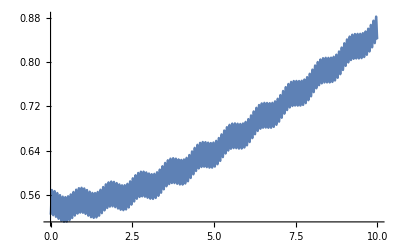

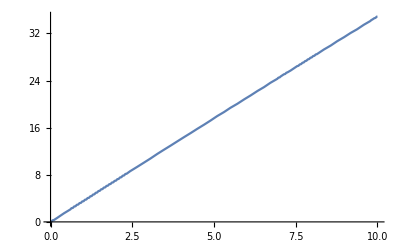

```mathematica
SolutionForced = Flatten@NDSolve[EquationForced /. {w ->2*Pi*0.535, hz -> 100 }, {θ[t], ϕ[t], ψ[t]}, {t, 0, 10}];
θForced[t_] = θ[t]/. SolutionForced;
ϕForced[t_] =ϕ[t]/. SolutionForced;
ψForced[t_] =ψ[t]/. SolutionForced;
Plot[θForced[t], {t, 0, 10}, ImageSize->"Large"]
Plot[ϕForced[t], {t, 0, 10}, ImageSize->"Large"]
```

## Solving equations for the free gyroscope

```mathematica
EquationFree = {
(J1* Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-J1 D[θ[t],{t, 2}]-J3* Sin[θ[t]] D[ϕ[t],t]*D[ψ[t],t]-(J3 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2+g h m Sin[θ[t]]+(h^2 m Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-h^2 m D[θ[t],{t, 2}]==0,
-J1 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-J1 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+J3 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]+J3 Sin[θ[t]] D[ψ[t],t] D[θ[t],t]+J3 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]-J3 Cos[θ[t]] D[ψ[t],{t, 2}]-J3 D[ϕ[t],{t, 2}]-h^2 m Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-h^2 m Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]==0,
 J3 (Sin[θ[t]] D[ϕ[t],t] D[θ[t],t]-Cos[θ[t]] D[ϕ[t],{t, 2}]-D[ψ[t],{t, 2}])==0,
θ[0] == Mod[θForced[10], 2Pi],
ϕ[0] == Mod[ϕForced[10], 2Pi], 
ψ[0] == Mod[ψForced[10],  2Pi], 
θ'[0] ==Mod[ θForced'[10] , 2Pi],
ϕ'[0] ==Mod[ϕForced'[10], 2Pi] , 
ψ'[0] == Mod[ψForced'[10], 2Pi]
} // FullSimplify
```

{1. Sin[θ[t]] ϕ'[t] ψ'[t]+7.65838 θ''[t]==2090.2 Sin[θ[t]]+3.32919 Sin[2 θ[t]] ϕ'[t]^2,θ'[t] (-0.000366211 Sin[2 θ[t]] ϕ'[t]+0.000055 Sin[θ[t]] ψ'[t])+(-0.000055-0.000366211 Sin[θ[t]]^2) ϕ''[t]==0.000055 Cos[θ[t]] ψ''[t],1. Sin[θ[t]] θ'[t] ϕ'[t]==1. Cos[θ[t]] ϕ''[t]+1. ψ''[t],θ[0]==0.841685,ϕ[0]==3.47117,ψ[0]==4.14877,θ'[0]==0.174631,ϕ'[0]==1.06354,ψ'[0]==5.57466}

```mathematica
SolutionFree = Flatten@NDSolve[EquationFree /. {w ->2*Pi*0.535 }, {θ[t], ϕ[t], ψ[t]}, {t, 0, 300}];
```

```mathematica
θFree[t_] = θ[t]/. SolutionFree;
ϕFree[t_] = ϕ[t]/. SolutionFree;
ψFree[t_] = ψ[t]/. SolutionFree;
```

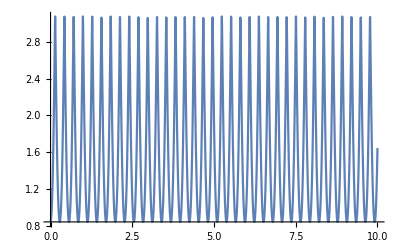

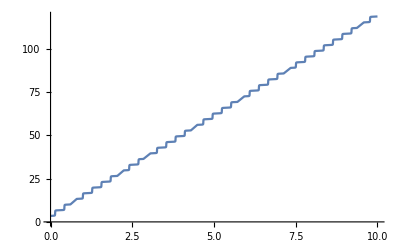

```mathematica
Plot[θFree[t], {t, 0, 10}, ImageSize->"Large"]
Plot[ϕFree[t], {t, 0, 10}, ImageSize->"Large"]
```